# Costruziazioni proposte dal dott. prof. Fassò™

## Sezione a.

```mathematica
f[μ_,x_]:=μ x(1-x)
```

```mathematica
orbita[μ_,x_,n_]:=NestList[f[μ,#]&,x,n]
```

```mathematica
graficoOrbita[μ_,x_,n_]:=Module[
{
pts=Table[{ξ,ξ},{ξ,NestList[f[μ,#]&,x,n]}]
},
Plot[{f[μ,t],t},{t,Min[x,0],Max[x,1]},PlotStyle->{{Black}},AspectRatio->Automatic,PlotRange->All,Epilog->{{Blue,Thin,Line[{First[#],{First[First@#],Last[Last@#]},Last[#]}]&/@Partition[pts,2,1]},{Red,Thick,Point/@Drop[pts,-1]},{Cyan,Thick,Point[pts//Last]}}]]
```

```mathematica
Manipulate[graficoOrbita[μ,x0,n],{{μ,1.1},0,4},{{x0,0.4},0,1},{{n,21},Range[1,1000,10]},Initialization:>{f[μ_,x_]:=μ x(1-x),graficoOrbita[μ_,x_,n_]:=Module[
{
pts=Table[{ξ,ξ},{ξ,NestList[f[μ,#]&,x,n]}]
},
Plot[{f[μ,t],t},{t,Min[x,0],Max[x,1]},PlotStyle->{{Black}},AspectRatio->Automatic,PlotRange->All,Epilog->{{Blue,Thin,Line[{First[#],{First[First@#],Last[Last@#]},Last[#]}]&/@Partition[pts,2,1]},{Red,Thick,Point/@Drop[pts,-1]},{Cyan,Thick,Point[pts//Last]}}]]}]
```

## Sezione b.

Dimostriamo la prima proposizione.

Fissato μ>0, dobbiamo risolvere l’equazione

x=μ x (1-x)

e possiamo risolverla con Mathematica

```mathematica
Solve[{μ>0,x==f[μ,x]},x,Reals]
```

{{x→ConditionalExpression[0, 0<μ<1||μ>1]},{x→ConditionalExpression[(-1+μ)/μ, 0<μ<1||μ>1]}}

La soluzione offerta da Mathematica tralascia il caso μ=1, che però si risolve facilmente perché l’unico punto fisso (con molteplicità doppia) è x=0.

```mathematica
Solve[x==f[1,x],x,Reals]
```

{{x→0},{x→0}}

Vediamo innanzitutto il caso x_0<0:

```mathematica
Reduce[{f[μ,x0]<x0,μ>0,x0<0},x0,Reals]
```

(0<μ≤1&&x0<(-1+μ)/μ)||(μ>1&&x0<0)

Si vede, dunque, che la successione f_μ^n(x_0) è monotona decrescente, a parte in un pezzetto in culo al prof; poiché l’immagine di una parabola concava non è inferiormente limitata, deduciamo che lim_(n→∞) f_μ^n(x_0)=-∞.

Passiamo al caso x_0>1:

```mathematica
Reduce[{f[μ,x0]<x0,μ>0,x0>1},x0,Reals]
```

μ>0&&x0>1

Ottenendo un risultato del tutto simile a quello precedente.

Dimostriamo la seconda proposizione.

Vediamo che

```mathematica
Reduce[{0≤x≤1,0≤f[μ,x]≤1,0<μ≤4},x]
```

0<μ≤4&&0≤x≤1

Vediamo che esiste un intorno di 1/2 che ha orbita divergente.

```mathematica
Reduce[{0≤x≤1,μ>4,0≤f[μ,x]≤1},x]
```

μ>4&&(0≤x≤1/2-1/2 √((-4+μ)/μ)||1/2+1/2 √((-4+μ)/μ)≤x≤1)

## Sezione c.

Creiamo un visualizzatore stupido del punto attrattivo in funzione di μ.

```mathematica
attrattivoPlot[nx_,n_,η_]:=With[{f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{0,4},{0,1}},
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

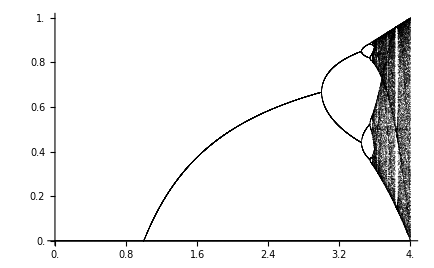

```mathematica
attrattivoPlot[30,10^4,10^4]
```

```mathematica
With[
{
f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)],
n=10^4,
η=10^4,
nx=30
},
Export[
"sas.csv",
Union@Flatten[
Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],
1
]
]
]
```

sas.csv

```mathematica
NSolve[x==f[μ,x],x]
```

```mathematica
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
```

```mathematica
g[μ_,n_]:=With[{x=Solve[{z==fn[μ,z,n],0<z≤1},z,Reals]⟦1,1,2⟧},D[fn[μ,ξ,n],ξ]/.{ξ:>x}]
```

```mathematica
g[3,2]
```

1

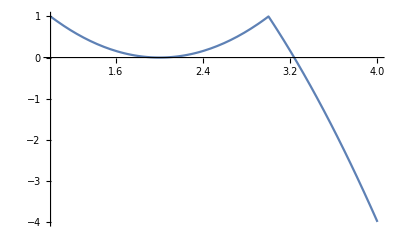

```mathematica
Plot[g[μ,2],{μ,1,4}]
```

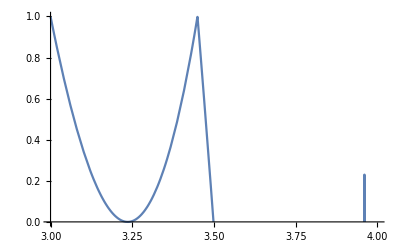

```mathematica
Plot[g[μ,4],{μ,3,4},PlotRange->{0,1}]
```

```mathematica
D[fn[3,x,2],x]/.x->2/3
```

1

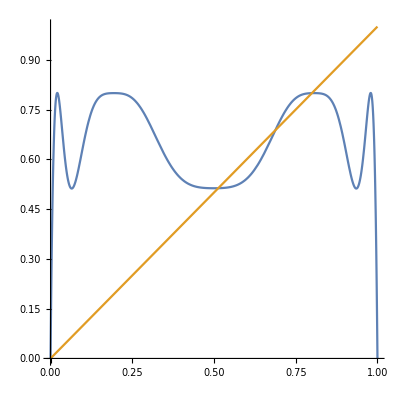

```mathematica
Plot[{fn[3.2,x,4],x},{x,0,1},AspectRatio->Automatic]
```

```mathematica
1.9/2.9
```

0.655172

```mathematica
Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]
```

```mathematica
DeleteCases[Drop[First/@Flatten[Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]/.Rule->List/.{x,y_}->y],1],_Root]
```

{(-1+μ)/μ,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2),(1+μ)/(2 μ)+1/2 √((-3-2 μ+μ^2)/μ^2)}

```mathematica
x[μ_]:=1-1/μ
x4[μ_]:=(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->x4[μ]}]
```

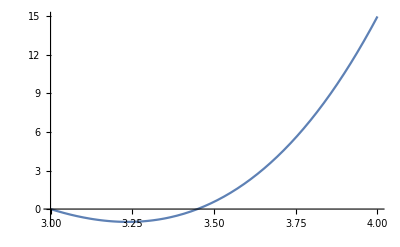

```mathematica
Plot[g[μ,4]-1.,{μ,3,4},PlotRange->Full]
```

```mathematica
Flatten[Solve[g[μ,4]==1,μ,Reals]/.Rule[μ,x_]->x]//Max
```

1+√6

```mathematica
Solve[{fn[μ,x,8]-x==0,μ>1+√6},x,Reals]
```

$Aborted

```mathematica
ClearAll[x]
```

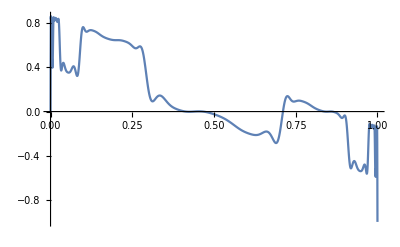

```mathematica
With[{μ=1+√6+10^-2},Plot[{fn[μ,ξ,8]-ξ},{ξ,0,1}]]
```

```mathematica
With[{μ=1+√6+$MachineEpsilon},FindRoot[{fn[μ,ξ,8]-ξ},{ξ,0.5}]]
```

{ξ→0.43996}

```mathematica
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->0.43996001699979026}]
```

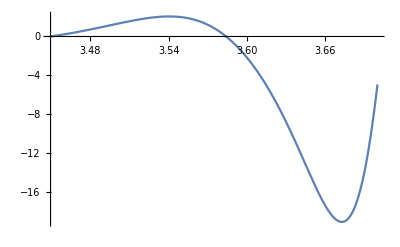

```mathematica
Plot[g[μ,8]-1,{μ,1+√6,3.7}]
```

```mathematica
FindRoot[FunctionInterpolation[g[μ,8]-1,{μ,1+√6,4}][μ],{μ,3.6}]
```

{μ→3.58402}